```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/manuscript/graphs

```mathematica
hbarc=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbarc)^2; (* MeV^-1 fm^-2*)
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
activeLEC=Select[Import["/home/kirscher/Documents/vault/Vorlesungen/num_methods/lec_ex0_b2.22.dat","Table"][[2;;]],#[[3]]!=-1.&];
line=Fit[Transpose[{activeLEC[[All,1]],activeLEC[[All,2]]}],{1,x},x];
fittedLECs=Table[{λ,line/.x->λ},{λ,Range[activeLEC[[All,1]][[1]],10 activeLEC[[All,1]][[-1]]]}];
activeLEC=activeLEC[[;;;;2]]
(*activeLEC=fittedLECs[[;;;;100]]*)
```

{{8.,-974.194,-1105.1,0.},{10.,-1206.46,-1256.76,0.},{12.,-1437.76,-1402.35,0.},{14.,-1668.47,-1537.32,0.},{16.,-1898.53,-1589.7,0.},{18.,-2128.1,-1711.48,4.29},{20.,-2357.36,-1788.28,4.46},{22.,-2586.19,-1845.33,0.},{24.,-2814.81,-1868.75,4.7},{26.,-3043.2,-1896.75,4.88},{28.,-3271.38,-1912.15,5.08},{30.,-3499.32,-1964.75,0.},{32.,-3727.18,-1971.84,0.},{34.,-3954.94,-1980.64,0.},{36.,-4182.67,-1919.66,0.},{38.,-4409.67,-1973.3,5.62},{40.,-4637.06,-1980.96,0.},{42.,-4864.11,-1925.1,0.}}

```mathematica
(*one dimer to rule them all*)
eCore=2.2;
ScaleFac=12.5;
dimerCore=Get["UnivDimerWF"]
dimerCore=Transpose[{dimerCore[[All,1]],ScaleFac dimerCore[[All,2]]}]
```

{{0.170746,0.0685723}}

{{0.170746,0.857153}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x=1/x (e^x-e^-x)/2
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

## ABAB

```mathematica
VlocABAB=Compile[{r,lam,Cc,Dd,Aa},Block[{eta2,eta3,w2,w3},
eta2=4 √2 Cc (Aa/(lam+2 Aa))^(3/2);
w2= 2lam Aa/(2 Aa+lam);
eta2 Exp[-w2 r^2]
]];

WnolocABAB=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,TwoMyOverHBsq},Block[{zeta1,zeta2,a1,c1,a2,c2,ex1,ex2,lamm=lam},
zeta1=-8 Aa^(3/2) (1/TwoMyOverHBsq);
a1=Aa;
c1=Aa;

zeta2=-32 √2 Cc Aa^3 (1/(2 Aa +lamm))^(3/2);

a2=Aa ((2 Aa+3 lam)/(2 Aa+lamm));
c2=Aa;

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

ex1=Exp[-a1 r^2-c1 rp^2];
ex2=Exp[-a2 r^2-c2 rp^2];

(-4 Pi r rp) (zeta1 ex1 (-(4 a1^2 r^2-2 a1)- TwoMyOverHBsq Ee)+zeta2 ex2)
]];
```

## ABAC

```mathematica
VlocABAC=Compile[{r,lam,Cc,Dd,Aa},Block[{eta2,w2,eta3,w3,eta4,w4},
eta2=6 √2 Cc (Aa/(lam+2 Aa))^(3/2);
w2= 2lam Aa/(2 Aa+lam);
eta3=8 Dd (Aa/(lam+2 Aa))^3;
w3= 4 lam Aa/(2 Aa+lam);
eta4=8 Dd Aa^3 (4 Aa^2+6 Aa lam+lam^2)^(-3/2);
w4= 4 lam Aa (Aa+lam)/(4 Aa^2+6 Aa lam+lam^2);
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]+eta4 Exp[-w4 r^2]
]];

WnolocABAC=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,TwoMyOverHBsq},Block[{zeta1,a1,c1,ex1,zeta2,a2,c2,ex2,zeta3,a3,b3,c3,ex3,zeta4,a4,b4,c4,ex4,zeta5,a5,b5,c5,ex5,lamm=lam},
zeta1=-8 Aa^(3/2) (1/TwoMyOverHBsq);
a1=Aa;
c1=Aa;

zeta2=-32 √2 Cc Aa^3 (1/(2 Aa +lamm))^(3/2);
a2=Aa ((2 Aa+3 lam)/(2 Aa+lamm));
c2=Aa;

zeta3=-8 Cc Aa^(3/2);
a3=Aa+lamm;c3=a3;
b3=2 lamm;

zeta4=-8 Dd Aa^3 (Aa+lamm)^(-3/2);
a4=(2 Aa^2+4 Aa lamm+lamm^2)/(2 (Aa+lamm));c4=a4;
b4=lamm^2 (Aa+lamm)^(-1);

zeta5=-16 √2 Dd Aa^3 (2 Aa+lamm)^(-3/2);
a5=(2 Aa^2+5 Aa lamm+lamm^2)/(2 Aa+lamm);
b5=2 lamm;
c5=(Aa+lamm);

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

ex1=Exp[-a1 r^2-c1 rp^2];
ex2=Exp[-a2 r^2-c2 rp^2];
ex3=Exp[-a3 r^2-b3 r rp-c3 rp^2];
ex4=Exp[-a4 r^2-b4 r rp-c4 rp^2];
ex5=Exp[-a5 r^2-b5 r rp-c5 rp^2];

(-4 Pi r rp) (zeta1 ex1 (-(4 a1^2 r^2-2 a1)- TwoMyOverHBsq Ee)+zeta2 ex2+zeta3 ex3+zeta4 ex4+zeta5 ex5)
]];
```

## ABCD

```mathematica
VlocABCD=Compile[{r,lam,Cc,Dd,Aa},Block[{eta2,w2,eta3,w3,eta4,w4},
eta2=8 √2 Cc (Aa/(lam+2 Aa))^(3/2);
w2= 2lam Aa/(2 Aa+lam);
eta3=16 Dd (Aa/(lam+2 Aa))^3;
w3= 4 lam Aa/(2 Aa+lam);
eta4=16 Dd Aa^3 (4 Aa^2+6 Aa lam+lam^2)^(-3/2);
w4= 4 lam Aa (Aa+lam)/(4 Aa^2+6 Aa lam+lam^2);
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]+eta4 Exp[-w4 r^2]
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocABAC[i hDif,lam,c0,d0,a00[[1]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocABAC[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[1]][[2]],TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}];

Wmat=(amat+wmat);

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];
relerr=Norm[Amat.usol-bcol]/Norm[usol];
(*Print["relative error in wave-function solution = ",relerr];*)

(*tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);*)
sol=NSolve[usol⟦-1⟧==RiccatiBesselJ[momentum Rdis,Lin]-RiccatiBesselN[momentum Rdis,Lin] xx,xx,Reals];
tanDelta=xx/.sol[[-1]];
t2=AbsoluteTime[];
(*Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins     p_match·r_max = ",momentum Rdis];*)
{tanDelta,usol}
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,LECd_,energ_:0.001]:=Module[{locall=l},
momFM=Sqrt[mh2 energ];
{TanDelSwave,wfkt}=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
{-TanDelSwave/Sqrt[mh2 energ ],wfkt}
]
```

alternative to the stochastic and inefficient search for an appropriate basis, one can invoke a genetic optimization (external Python/Fortran program, look for <bridgeA2_tmp.py> and calls therein)
and feed the results to the function <CalcDimerE[]> (see above

Using λ=8.fm^-2     C=-974.194MeV  which is renormalized to B(dimer)=2.2MeV

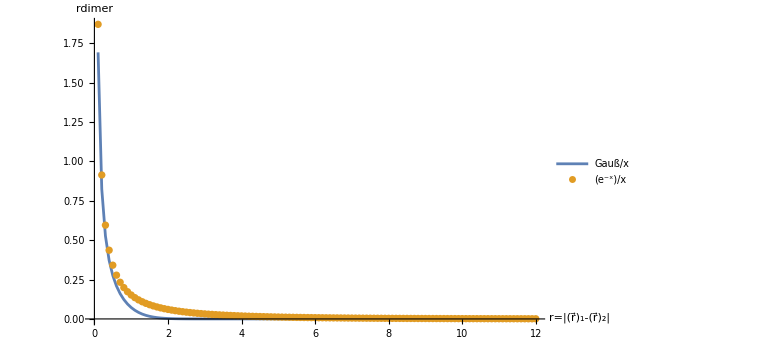

```mathematica
lambdas=activeLEC[[All,1]];
lambdaTest=lambdas[[1]];
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
Print["Using λ=",Style[lambdaTest,Red],"fm^-2     C=",Style[LECc,Red],"MeV  which is renormalized to B(dimer)=",Style[eCore,Red],"MeV"];

JacobiTrailWavefunctionU=Total[#[[1]] Exp[-#[[2]] r1^2]&/@dimerCore];rR=Range[0.1,12,0.100];
JacobiTrailWavefunctionDataU=Table[R1^-1 JacobiTrailWavefunctionU/.{r1->R1},{R1,rR}];

plotData=Transpose[{rR,JacobiTrailWavefunctionDataU}];
plotDataExp=Table[{rr,√((√(Mm eCore))/(2 π hbarc))Exp[-(√(Mm eCore))/hbarc rr] rr^-1},{rr,rR}];
lgd={"Gauß/x","e^-x/x"};

ListPlot[{Transpose[{rR,plotData[[All,2]]}],Transpose[{rR,plotDataExp[[All,2]]}]},AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large,PlotLabels->Automatic,Joined->{True,False},PlotRange->All]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.1;
(* Integration grid *)
rMa=12;
grdPerFermi=13;
nGrd=IntegerPart[rMa grdPerFermi];
results={};

Do[

LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lam&]][[3]];

tmp=GetEREP3[lam,rMa,nGrd,dimerCore,LECc,LECd,energ][[1]];
AppendTo[results,{lam,LECc,rMa,nGrd,eCore,tmp,tmp/(hbarc/√(Mm Abs[eCore]))}];
Print["λ=",lam," B(2)=",eCore,"  C_0(λ)=",LECc,")  ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbarc/√(Mm Abs[eCore]))];
,{lam,lambdas}];
```

λ=8. B(2)=2.2  C_0(λ)=-974.194)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=-6.27778 ; a_dd/a_aa=-1.44588

λ=10. B(2)=2.2  C_0(λ)=-1206.46)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=0.791456 ; a_dd/a_aa=0.182285

λ=12. B(2)=2.2  C_0(λ)=-1437.76)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.13139 ; a_dd/a_aa=0.260578

λ=14. B(2)=2.2  C_0(λ)=-1668.47)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.26009 ; a_dd/a_aa=0.290219

λ=16. B(2)=2.2  C_0(λ)=-1898.53)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.33201 ; a_dd/a_aa=0.306783

λ=18. B(2)=2.2  C_0(λ)=-2128.1)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.37893 ; a_dd/a_aa=0.31759

λ=20. B(2)=2.2  C_0(λ)=-2357.36)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.41335 ; a_dd/a_aa=0.325516

λ=22. B(2)=2.2  C_0(λ)=-2586.19)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.44014 ; a_dd/a_aa=0.331689

λ=24. B(2)=2.2  C_0(λ)=-2814.81)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.46191 ; a_dd/a_aa=0.336701

λ=26. B(2)=2.2  C_0(λ)=-3043.2)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.4801 ; a_dd/a_aa=0.34089

λ=28. B(2)=2.2  C_0(λ)=-3271.38)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.49567 ; a_dd/a_aa=0.344478

λ=30. B(2)=2.2  C_0(λ)=-3499.32)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.50923 ; a_dd/a_aa=0.3476

λ=32. B(2)=2.2  C_0(λ)=-3727.18)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.52121 ; a_dd/a_aa=0.35036

λ=34. B(2)=2.2  C_0(λ)=-3954.94)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.53191 ; a_dd/a_aa=0.352824

λ=36. B(2)=2.2  C_0(λ)=-4182.67)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.54156 ; a_dd/a_aa=0.355047

λ=38. B(2)=2.2  C_0(λ)=-4409.67)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.55036 ; a_dd/a_aa=0.357072

λ=40. B(2)=2.2  C_0(λ)=-4637.06)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.55837 ; a_dd/a_aa=0.358918

λ=42. B(2)=2.2  C_0(λ)=-4864.11)  ; R_max=12 ; #=156 ; E_match=0.1 ; a_dd=1.56576 ; a_dd/a_aa=0.360621

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

λ = 8.   C_0(λ) = -974.194     R_max = 44     #(grid points) = 616                a_dd = -5.91611 fm        a_dd/a_aa = -1.36258

λ = 10.   C_0(λ) = -1206.46     R_max = 44     #(grid points) = 616                a_dd = 0.794511 fm        a_dd/a_aa = 0.182989

λ = 12.   C_0(λ) = -1437.76     R_max = 44     #(grid points) = 616                a_dd = 1.13227 fm        a_dd/a_aa = 0.260781

λ = 14.   C_0(λ) = -1668.47     R_max = 44     #(grid points) = 616                a_dd = 1.26052 fm        a_dd/a_aa = 0.290318

λ = 16.   C_0(λ) = -1898.53     R_max = 44     #(grid points) = 616                a_dd = 1.33227 fm        a_dd/a_aa = 0.306844

λ = 18.   C_0(λ) = -2128.1     R_max = 44     #(grid points) = 616                a_dd = 1.37911 fm        a_dd/a_aa = 0.317632

λ = 20.   C_0(λ) = -2357.36     R_max = 44     #(grid points) = 616                a_dd = 1.41348 fm        a_dd/a_aa = 0.325548

λ = 22.   C_0(λ) = -2586.19     R_max = 44     #(grid points) = 616                a_dd = 1.44025 fm        a_dd/a_aa = 0.331714

λ = 24.   C_0(λ) = -2814.81     R_max = 44     #(grid points) = 616                a_dd = 1.462 fm        a_dd/a_aa = 0.336722

λ = 26.   C_0(λ) = -3043.2     R_max = 44     #(grid points) = 616                a_dd = 1.48017 fm        a_dd/a_aa = 0.340908

λ = 28.   C_0(λ) = -3271.38     R_max = 44     #(grid points) = 616                a_dd = 1.49574 fm        a_dd/a_aa = 0.344493

λ = 30.   C_0(λ) = -3499.32     R_max = 44     #(grid points) = 616                a_dd = 1.50929 fm        a_dd/a_aa = 0.347613

λ = 32.   C_0(λ) = -3727.18     R_max = 44     #(grid points) = 616                a_dd = 1.52126 fm        a_dd/a_aa = 0.350372

λ = 34.   C_0(λ) = -3954.94     R_max = 44     #(grid points) = 616                a_dd = 1.53196 fm        a_dd/a_aa = 0.352835

λ = 36.   C_0(λ) = -4182.67     R_max = 44     #(grid points) = 616                a_dd = 1.54161 fm        a_dd/a_aa = 0.355057

λ = 38.   C_0(λ) = -4409.67     R_max = 44     #(grid points) = 616                a_dd = 1.55039 fm        a_dd/a_aa = 0.357081

λ = 40.   C_0(λ) = -4637.06     R_max = 44     #(grid points) = 616                a_dd = 1.55841 fm        a_dd/a_aa = 0.358926

λ = 42.   C_0(λ) = -4864.11     R_max = 44     #(grid points) = 616                a_dd = 1.5658 fm        a_dd/a_aa = 0.360629

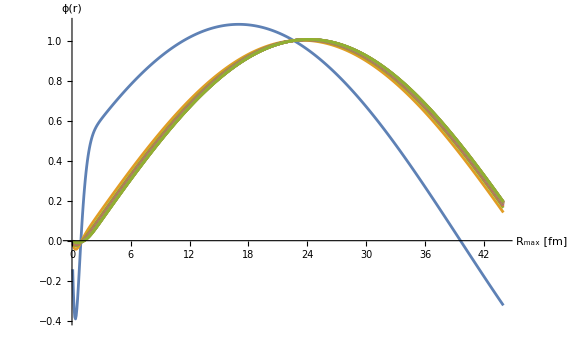

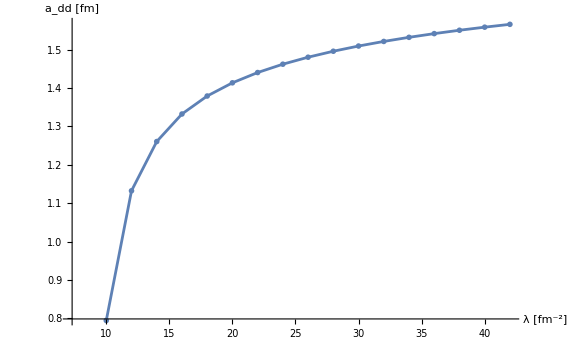

```mathematica
grdPerFermi=14;
rMa=44;
nGrd=IntegerPart[rMa grdPerFermi];
Grd=Range[0,rMa,1/grdPerFermi][[2;;]];

results={};
resultsWF={};
runtimes={};

(*SetSharedVariable[results,resultsPhases];*)
Do[

LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lam&]][[3]];
ta=AbsoluteTime[];
{tmp,tmp2}=GetEREP3[lam,rMa,nGrd,dimerCore,LECc,LECd,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[resultsWF,Transpose[{Grd,tmp2}]];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["λ = ",lam,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbarc/√(Mm Abs[eCore])),Red,18]];
,{lam,lambdas}]

ListPlot[resultsWF,Joined->True,PlotRange->Full,ImageSize->Large,AxesLabel->{"R_max [fm]","ϕ(r)"}]
ListPlot[Transpose[{lambdas,results}],Joined->True,PlotMarkers->"OpenMarkers",AxesLabel->{"λ [fm^-2]","a_dd [fm]"}]
```

1.1

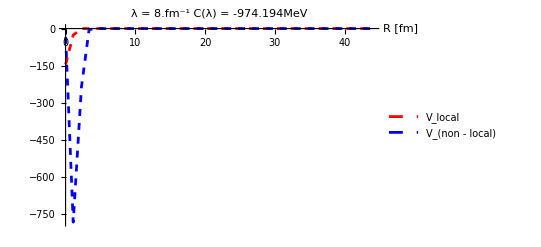

-Graphics3D-

```mathematica
rP=1.1
lam=lambdas[[1]];
LECc=Flatten[Select[activeLEC,#[[1]]==lam&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==lam&]][[3]];

Plot[
{VlocABAB[R,lam,LECc,LECd,dimerCore[[1]][[2]]],Re[WnolocABAB[R,rP,energ,lam,LECc,LECd,dimerCore[[1]][[2]],mh2]]},{R,0.01,rMa},PlotPoints->40,MaxRecursion->0,PlotLegends->{"V_local","V_(non - local)"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black}},AxesLabel->{"R [fm]"},PlotLabel->"λ = "<>ToString[lam]<>"fm^-1    C(λ) = "<>ToString[LECc]<>"MeV",PlotRange->Full]

Plot3D[Re[WnolocABAB[rr,rp,energ,lam,LECc,LECd,dimerCore[[1]][[2]],mh2]],{rr,0.01,rMa},{rp,0.01,rMa},PlotRange->Full]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = -5.99976     a_dd/a_aa = -1.38184

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 0.722884     a_dd/a_aa = 0.166492

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.06043     a_dd/a_aa = 0.244235

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.18857     a_dd/a_aa = 0.273748

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.26026     a_dd/a_aa = 0.290259

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.30706     a_dd/a_aa = 0.301038

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.3414     a_dd/a_aa = 0.308946

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.36815     a_dd/a_aa = 0.315106

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.38987     a_dd/a_aa = 0.320109

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.40803     a_dd/a_aa = 0.324291

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.42357     a_dd/a_aa = 0.327872

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.43711     a_dd/a_aa = 0.33099

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.44907     a_dd/a_aa = 0.333746

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.45976     a_dd/a_aa = 0.336206

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.4694     a_dd/a_aa = 0.338426

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.47818     a_dd/a_aa = 0.340448

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.48618     a_dd/a_aa = 0.342291

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

a_dd = 1.49356     a_dd/a_aa = 0.343992

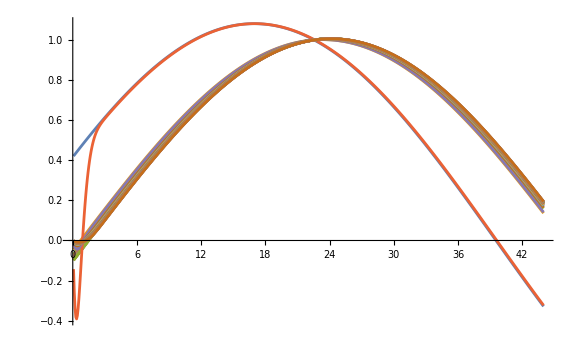

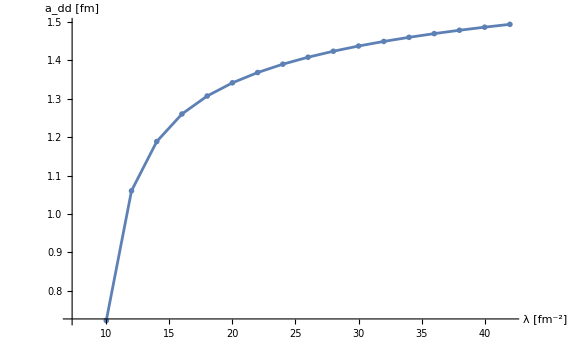

```mathematica
momFM=Sqrt[mh2 energ];
rRan=Range[0,rMa,1/grdPerFermi];
match1=1;
match2=5;
resultsadd={};
riccatis={};
Do[

sol=NSolve[{resultsWF[[nres]][[All,2]][[-match1]]==nm (RiccatiBesselJ[momFM (rMa-match1/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMa-match1/grdPerFermi),0]),
resultsWF[[nres]][[All,2]][[-match2]]==nm (RiccatiBesselJ[momFM (rMa-match2/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMa-match2/grdPerFermi),0])},{nm,tandd},Reals];

RiccatiBJN=Table[(nm (RiccatiBesselJ[momFM r,0]-tandd RiccatiBesselN[momFM r,0])),{r,rRan}];
RiccatiBJN=RiccatiBJN/.sol[[1]];
AppendTo[riccatis,Transpose[{rRan,RiccatiBJN}]];

add=(-tandd/.sol[[1]][[2]])/Sqrt[mh2 energ ];
AppendTo[resultsadd,add];

Print["a_dd = ",add, "     a_dd/a_aa = ",add/(hbarc/√(Mm Abs[eCore])) ]
,{nres,Range[Length[lambdas]]}]
ListPlot[Join[riccatis,resultsWF],Joined->True,PlotRange->Full,ImageSize->Large]
ListPlot[Transpose[{lambdas,resultsadd}],Joined->True,PlotMarkers->"OpenMarkers",AxesLabel->{"λ [fm^-2]","a_dd [fm]"}]
```